```mathematica
(* Define functions for left and right Radau polynomials. *)
leftRadau[order_,x_]:=(LegendreP[order,x]+LegendreP[order-1,x])/2;
rightRadau[order_,x_]:=(-1)^order(LegendreP[order,x]-LegendreP[order-1,x])/2;
(* Define function for Lagrange polynomial. *)
Lagrange[xpts_,ypts_,x_]:=InterpolatingPolynomial[Transpose@{xpts,ypts},x];
```

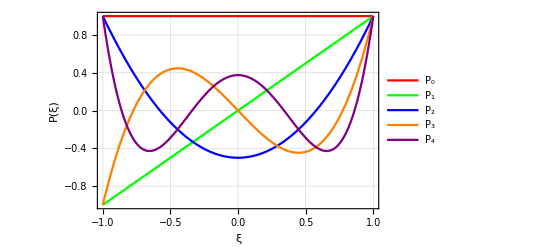

```mathematica
(* Plot Legendre polynomials order 0:4 in unit cell. *)
Plot[{LegendreP[0,x],LegendreP[1,x],LegendreP[2,x],LegendreP[3,x],LegendreP[4,x]},{x,-1,1.},AxesOrigin->{-1,-1},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{,},PlotStyle->{Red,Green,Blue,Orange,Purple},PlotLegends->{Subscript[P,0],Subscript[P,1],Subscript[P,2],Subscript[P,3],Subscript[P,4]}]
```

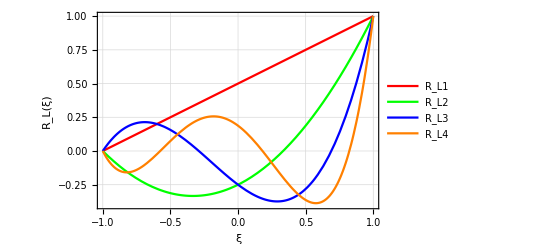

```mathematica
(* Plot left Radau polynomials order 0:4 in unit cell. *)
Plot[{leftRadau[1,x],leftRadau[2,x],leftRadau[3,x],leftRadau[4,x]},{x,-1,1.},PlotRange->{-.4,1.},AxesOrigin->{-1,-1},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{,},PlotStyle->{Red,Green,Blue,Orange,Purple},PlotLegends->{Subscript[R,L1],Subscript[R,L2],Subscript[R,L3],Subscript[R,L4]}]
```

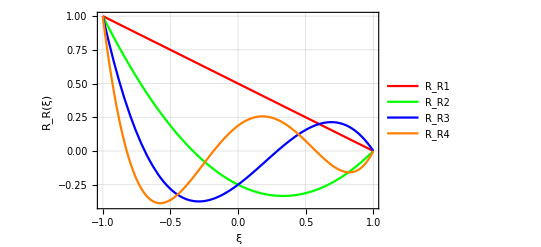

```mathematica
(* Plot right Radau polynomials order 0:4 in unit cell. *)
Plot[{rightRadau[1,x],rightRadau[2,x],rightRadau[3,x],rightRadau[4,x]},{x,-1,1.},PlotRange->{-.4,1.},AxesOrigin->{-1,-1},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{,},PlotStyle->{Red,Green,Blue,Orange,Purple},PlotLegends->{Subscript[R,R1],Subscript[R,R2],Subscript[R,R3],Subscript[R,R4]}]
```

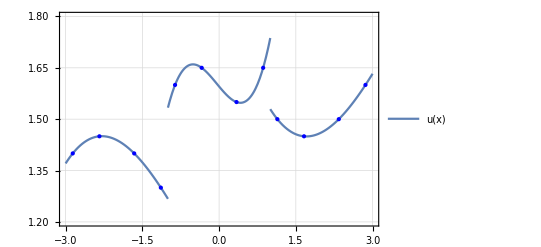

```mathematica
(* Flux reconstruction example for Burgers equation. *)
order=3;
(* Gauss points defined by zeros of Legendre polynomial. *)
roots=Sort[Simplify[x/. Solve[LegendreP[order+1,x]==0,x]]];
xgauss=Sort[roots//N[#,5]&];
(* Solution point locations in each cell. *)
xcell1=xgauss-2;
xcell2=xgauss;
xcell3=xgauss+2;
(* Solution point values in each cell. *)
ucell1={1.4,1.45,1.4,1.3};
ucell2={1.6,1.65,1.55,1.65};
ucell3={1.5,1.45,1.5,1.6};
(* Discontinuous flux function for Burgers equation. *)
fdcell1=ucell1^2;
fdcell2=ucell2^2;
fdcell3=ucell3^2;
(* Merge the {x,u} data into pairs for plotting. *)
datau1=Transpose@{xcell1,ucell1};
datau2=Transpose@{xcell2,ucell2};
datau3=Transpose@{xcell3,ucell3};
datafd1=Transpose@{xcell1,fdcell1};
datafd2=Transpose@{xcell2,fdcell2};
datafd3=Transpose@{xcell3,fdcell3};
(* Common flux, weighted toward upstream value. *)
(* Just for plotting, not the actual common flux. *)
fl=0.7*InterpolatingPolynomial[datafd1,-1]+0.3*InterpolatingPolynomial[datafd2,-1];
fr=0.7*InterpolatingPolynomial[datafd2,1]+0.3*InterpolatingPolynomial[datafd3,1];
(* Left correction function. *)
glcell2[order_,x_]:=(fl-InterpolatingPolynomial[datafd2,-1])rightRadau[order,x];
grcell2[order_,x_]:=(fr-InterpolatingPolynomial[datafd2,1])leftRadau[order,x];
gcell2[order_,x_]:=glcell2[order,x]+grcell2[order,x];
(* Continuous flux function. *)
fccell2[order_,x_]:=InterpolatingPolynomial[datafd2,x]+glcell2[order,x]+grcell2[order,x];
datafl={-1,fl};
datafr={1,fr};
(* ListPlot can be used to view solution points. *)
ListPlot[{datau1,datau2,datau3},PlotRange->{{-3,3},{1.2,1.8}},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}];
(* Create plots of solution points in each cell. *)
plotu1p=Graphics[{PointSize[Medium],Blue,Point[datau1]}];
plotu2p=Graphics[{PointSize[Medium],Blue,Point[datau2]}];
plotu3p=Graphics[{PointSize[Medium],Blue,Point[datau3]}];
(* Create plots of solution polynomials in each cell. *)
plotu1=Plot[InterpolatingPolynomial[datau1,x],{x,-3,-1},PlotLegends->{}];
plotu2=Plot[InterpolatingPolynomial[datau2,x],{x,-1,1}];
plotu3=Plot[InterpolatingPolynomial[datau3,x],{x,1,3}];
(* Combine plots of solution points and polynomials. *)
Show[plotu1,plotu2,plotu3,plotu1p,plotu2p,plotu3p,PlotRange->{{-3,3},{1.2,1.8}},AxesOrigin->{-3,0.2},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}]
```

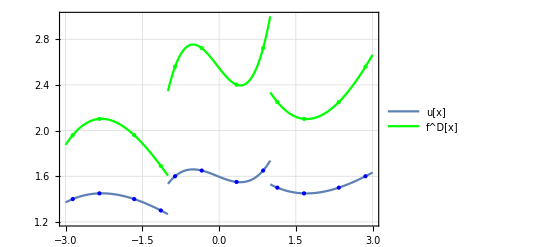

```mathematica
(* Create plots of discontinuous flux points in each cell. *)
plotfd1p=Graphics[{PointSize[Medium],Green,Point[datafd1]}];
plotfd2p=Graphics[{PointSize[Medium],Green,Point[datafd2]}];
plotfd3p=Graphics[{PointSize[Medium],Green,Point[datafd3]}];
(* Create plots of discontinuous flux polynomials in each cell. *)
plotfd1=Plot[InterpolatingPolynomial[datafd1,x],{x,-3,-1},PlotStyle->{Green},PlotLegends->{}];
plotfd2=Plot[InterpolatingPolynomial[datafd2,x],{x,-1,1},PlotStyle->{Green}];
plotfd3=Plot[InterpolatingPolynomial[datafd3,x],{x,1,3},PlotStyle->{Green}];
(* Combine plots of solution points and polynomials. *)
Show[plotu1,plotu2,plotu3,plotu1p,plotu2p,plotu3p,plotfd1,plotfd2,plotfd3,plotfd1p,plotfd2p,plotfd3p,PlotRange->{{-3,3},{1.2,3.0}},AxesOrigin->{-3,0.2},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}]
```

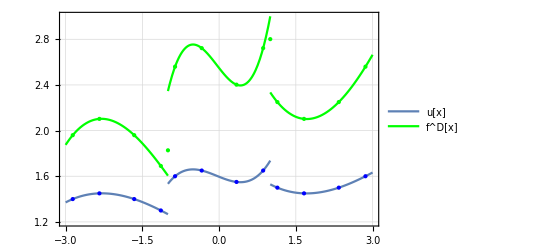

```mathematica
(* Create plots of common flux points in middle cell. *)
plotflp=Graphics[{PointSize[Medium],Green,Point[datafl]}];
plotfrp=Graphics[{PointSize[Medium],Green,Point[datafr]}];
(* Combine plots of solution points and polynomials. *)
Show[plotu1,plotu2,plotu3,plotu1p,plotu2p,plotu3p,plotfd1,plotfd2,plotfd3,plotfd1p,plotfd2p,plotfd3p,plotflp,plotfrp,PlotRange->{{-3,3},{1.2,3.0}},AxesOrigin->{-3,0.2},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}]
```

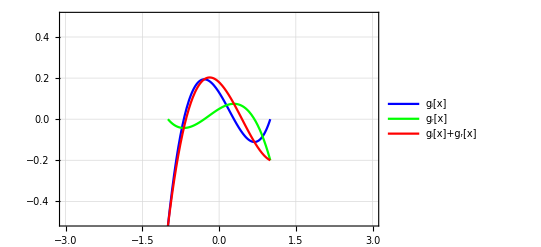

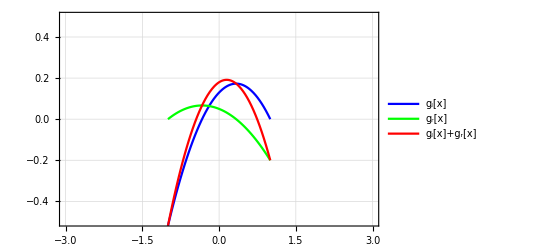

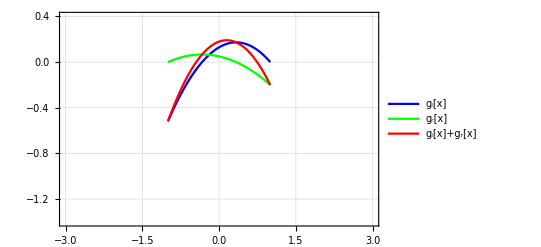

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Create plots of flux correction polynomials in middle cell. *)
plotgl=Plot[glcell2[order,x],{x,-1,1},PlotStyle->{Blue},PlotLegends->{}];
plotgr=Plot[grcell2[order,x],{x,-1,1},PlotStyle->{Green},PlotLegends->{}];
plotg=Plot[gcell2[order,x],{x,-1,1},PlotStyle->{Red},PlotLegends->{+}];
Show[plotgl,plotgr,plotg,PlotRange->{{-3,3},{-.5,.5}},AxesOrigin->{-3,-1.4},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}]
```

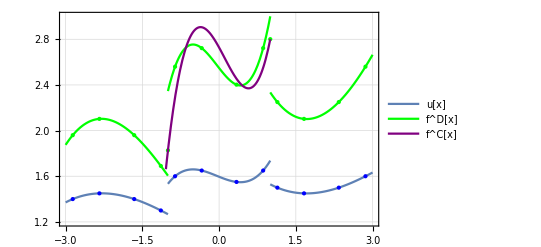

```mathematica
(* Create plots of continuous flux polynomial in middle cell. *)
plotfc=Plot[fccell2[order,x],{x,-1.16,1},PlotStyle->{Purple},PlotLegends->{}];
(* Combine plots of solution points and polynomials. *)
Show[plotu1,plotu2,plotu3,plotu1p,plotu2p,plotu3p,plotfd1,plotfd2,plotfd3,plotfd1p,plotfd2p,plotfd3p,plotflp,plotfrp,plotfc,PlotRange->{{-3,3},{1.2,3.0}},AxesOrigin->{-3,0.2},GridLines->Automatic,Frame->{True,True,True,True},FrameLabel->{}]
```